```mathematica
Quit
```

```mathematica
data={
Labeled[{1.7 10^(-27),10^(-15)},"proton"],
Labeled[{1.7 10^(-27),5 10^(-11)},"H atom"],
Labeled[{10^(-15),10^(-6)},"bacterium"],
Labeled[{80,2},"person"],
Labeled[{6 10^24,10^7},"earth"],
Labeled[{2 10^30,10^13},"solar system"],
Labeled[{2 10^42,10^18},"Milky Way"]
};
```

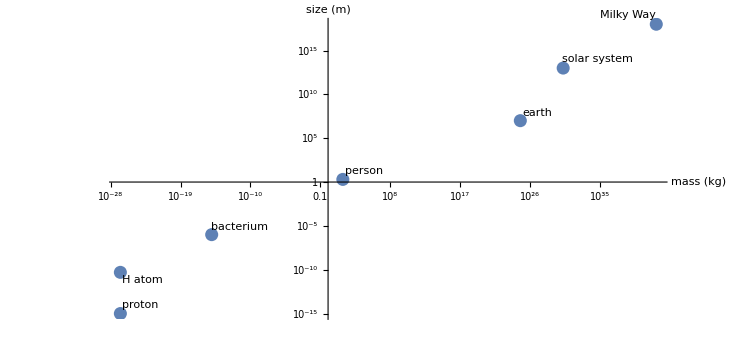

```mathematica
LLplot=ListLogLogPlot[data,AxesLabel->{"mass (kg)","size (m)"},AspectRatio->Automatic,AxesOrigin->{1,1}]
```

```mathematica
water=LogLogPlot[(mass^(1/3))/10,{mass,10^(-31),10^45},PlotStyle->Green];
```

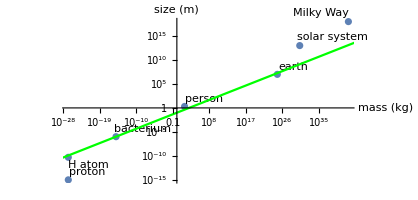

```mathematica
Show[LLplot,water]
```

```mathematica
more={
Labeled[{1.6 10^(-25),10^(-14)},"U nucleus"],
Labeled[{1.5 10^(-25),4 10^(-10)},"U atom"],
Labeled[{10^(-18),10^(-7)},"virus"],
Labeled[{4 10^8,400},"empire state"],
Labeled[{2 10^30,1.4 10^9},"sun"],
Labeled[{1.5 10^32,5 10^5},"small BH"],
Labeled[{10^37,3 10^10},"supermassive BH"],
Labeled[{400000,200},"train"],
Labeled[{2 10^14,10^4},"comet"],
Labeled[{10^27,10^8},"Jupiter"],
Labeled[{10^(-30),10^(-19)},"up quark"],
Labeled[{10^(-26),10^(-10)},"C atom"],
Labeled[{10^22, 10^6},"Pluto"],
Labeled[{4 10^(-27),3.5 10^(-10)},"Fr atom"],
Labeled[{1.5 10^5,30},"blue whale"],
Labeled[{10^44,10^22},"galaxy cluster"],
Labeled[{10^(-14),10^(-6)},"blood cell"],
Labeled[{2 10^(-8),7 10^(-35)},"Planck"]
};
```

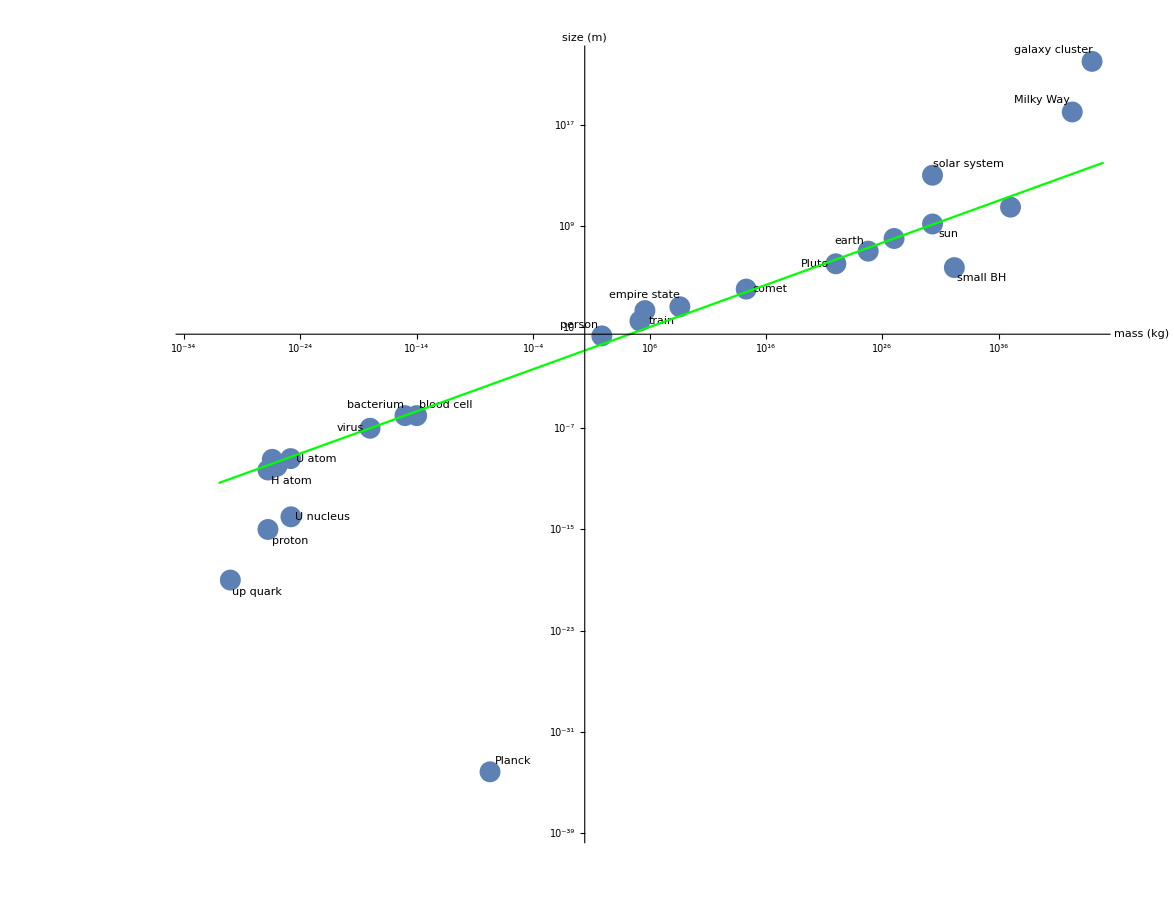

```mathematica
Show[ListLogLogPlot[Join[data,more],AxesLabel->{"mass (kg)","size (m)"},AspectRatio->Automatic],water,AxesOrigin->{1,1}]
```

```mathematica
Compton=LogLogPlot[2 10^(-42)/mass,{mass,10^(-31),10^(-5)},PlotStyle->Red];
```

```mathematica
Schwarzschild=LogLogPlot[3 10^(-27)mass,{mass,10^(-10),10^45},PlotStyle->Black];
```

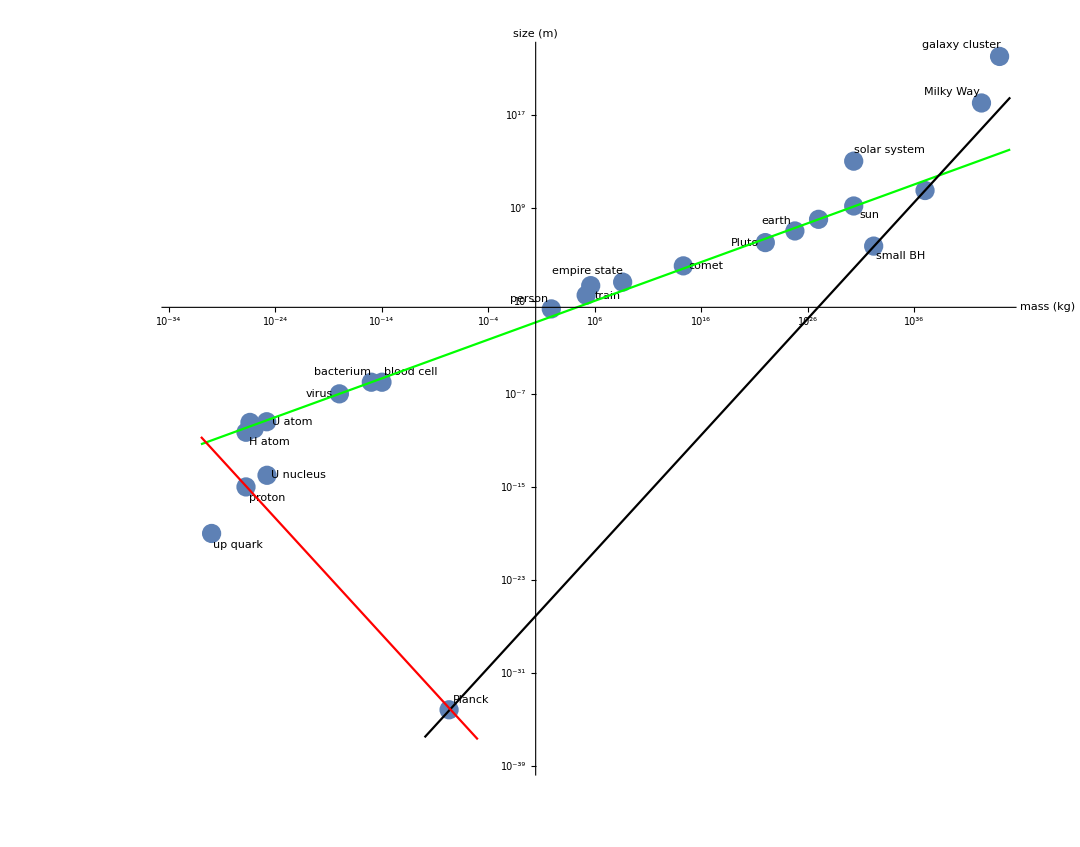

```mathematica
Show[ListLogLogPlot[Join[data,more],AxesLabel->{"mass (kg)","size (m)"},AspectRatio->Automatic],water,Schwarzschild,Compton,AxesOrigin->{1,1}]
```